```mathematica
(* Stokes Parameter and how th estate of light can be read. *)
```

```mathematica
{a,b}{c,d}
```

{a c,b d}

```mathematica
(* Input Light *)
```

```mathematica
Ein={Cos[60 °],Sin[60 °]} Exp[ⅈ t];
```

```mathematica
(* measurement *)
```

```mathematica
P000={1,0};
P045={1,1}/√2;
P090={0,1};
P135={1,-1}/√2;
PQ={ⅈ,1};
```

```mathematica
I000=1/2(Ein.P000)Simplify[Conjugate[(Ein.P000)],Element[t,Reals]]//Expand//Simplify;(* I000 *)
I045=1/2(Ein.P045)Simplify[Conjugate[(Ein.P045)],Element[t,Reals]]//Expand//Simplify;(* I045 *)
I090=1/2(Ein.P090)Simplify[Conjugate[(Ein.P090)],Element[t,Reals]]//Expand//Simplify;(* I090 *)
I135=1/2(Ein.P135)Simplify[Conjugate[(Ein.P135)],Element[t,Reals]]//Expand//Simplify;(* I135 *)
I045Q=1/2((Ein PQ).P045)Simplify[Conjugate[(Ein PQ).P045],Element[t,Reals]]//Expand//Simplify;(* I045Q *)
I135Q=1/2((Ein PQ).P135)Simplify[Conjugate[(Ein PQ).P135],Element[t,Reals]]//Expand//Simplify;(* I135Q *)
{I000,I045,I090,I135,I045Q,I135Q}//N
S0= I000+I090;
S1=I000-I090;
S2=I045-I135;
S3=I045Q-I135Q;
{S0, S1, S2, S3}//N
P=(√(S1^2+S2^2+S3^2))/S0;
χ=1/2 ArcTan[S3/(√(S1^2+S2^2)+0.000001)]*180/π;
ψ=1/2 ArcTan[S2/(S1+0.0000000001)]*180/π;
{P,χ,ψ}//N
```

{0.125,0.466506,0.375,0.0334936,0.25,0.25}

{0.5,-0.25,0.433013,0.}

{1.,0.,-30.}

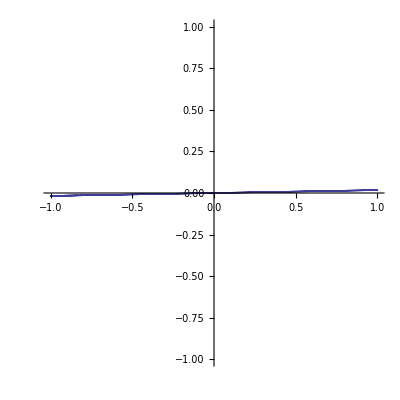

```mathematica
Ed={ Cos[χ π/180] Cos[t]Cos[ψ π/180]-Sin[χ π/180]Sin[t]Sin[ψ π/180], Sin[χ π/180]Sin[t]Cos[ψ π/180]+ Cos[χ π/180] Cos[t]Sin[ψ π/180]};
ParametricPlot[Ed,{t,0,10},PlotRange->1]
```

```mathematica
Iout[P_,Q_,Ein_]:=1/2((Ein Q).P)Simplify[Conjugate[((Ein Q).P)],Element[t,Reals]]//Expand//Simplify;
```

```mathematica
A[P_,Q_,ϕ_]:=Iout[P,Q,{Cos[ϕ °],Sin[ϕ °]}]
```

```mathematica
K[Ang_]:=
{A[P000,1,Ang[[1]]],A[P045,1,Ang[[2]]],A[P090,1,Ang[[3]]],A[P135,1,Ang[[4]]],A[P045,PQ,Ang[[5]]],A[P135,PQ,Ang[[6]]]}
```

```mathematica
S[K_]:={K[[1]]+K[[3]],K[[1]]-K[[3]],K[[2]]-K[[4]],K[[5]]-K[[6]]}
```

```mathematica
Q[S_]:={(√(S[[2]]^2+S[[3]]^2+S[[4]]^2))/S[[1]],1/2 ArcTan[S[[4]]/(√(S[[2]]^2+S[[3]]^2)+0.000001)]*180/π,1/2 ArcTan[S[[3]]/(S[[2]]+0.0000000001)]*180/π}//N
```

```mathematica
Ang={1,1,1,-1,-1,-1}+0;
J=Q[S[K[Ang]]]
P=J[[1]];
χ=J[[2]];
ψ=J[[3]];
{Mean[Ang],StandardDeviation[Ang]}//N
```

{0.999391,0.,0.}

{0.,1.09545}

```mathematica
Ang=Permutations[{1,1,1,-1,-1,-1}];
Length[Ang]
```

20

```mathematica
U=Table[J=Q[S[K[Ang[[i]]+22]]],{i,1,20}]//MatrixForm;
AOP=Table[U[[1,i]][[3]],{i,1,20}];
DOP=Table[U[[1,i]][[1]],{i,1,20}];
{Max[AOP],Min[AOP],(Max[AOP]-Min[AOP])/2,Mean[AOP],StandardDeviation[AOP]}
{Max[DOP],Min[DOP],(Max[DOP]-Min[DOP])/2,Mean[DOP],StandardDeviation[DOP]}
```

{22.5087,21.4732,0.517761,21.9996,0.325283}

{1.04226,0.958872,0.0416932,0.999805,0.0274871}

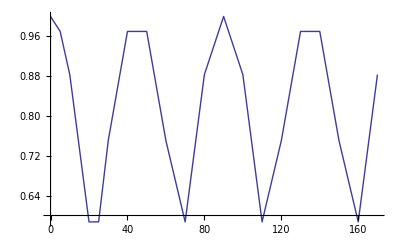

```mathematica
ListLinePlot[{{0,1},
{5,0.969904},
{10,0.883212},
{20,0.587154},
{25,0.587145},
{30,0.750305},
{40,0.969904},
{50,0.969904},
{60,0.750305},
{70,0.587154},
{80,0.883212},
{90,1},
{100,0.883212},
{110,0.587154},
{120,0.750305},
{130,0.969904},
{140,0.969904},
{150,0.750305},
{160,0.587154},
{170,0.883212}}]
```